Строим hyperhoneycomb решетку:

```mathematica
unitCell3D[x_,y_,z_]:={Red,Sphere[{x,y,z},0.1],Blue,Sphere[{x + 1/2,y+(√2)/2,z+3/2},0.1], Yellow, Sphere[{x, y, z+1}, 0.1], Green, Sphere[{x+1/2, y+(√2)/2, z+5/2},0.1], Gray,
Cylinder[{{x,y,z}, {x, y, z+1}}, 0.05],Cylinder[{{x, y, z+1}, {x + 1/2,y+(√2)/2,z+3/2}}, 0.05], Cylinder[{ {x + 1/2,y+(√2)/2,z+3/2}, {x+1/2, y+(√2)/2, z+5/2}}, 0.05],Cylinder[{{x,y,z}, {x+1/2,y+1/(√2)-√2,z-1/2}}, 0.05], Cylinder[{{x+1/2, y+(√2)/2, z+5/2}, {x+1,y,z+3}}, 0.05],
Cylinder[{{x, y, z+1},{x-1/2, y-1/(√2), z+3/2}}, 0.05]}
```

```mathematica
Graphics3D[Block[{unitVectA={0, √2, 3},unitVectB={1,0,3}, unitVectC = {1, √2, 0}},Table[unitCell3D@@(unitVectA j+unitVectB k + unitVectC i),{j,2},{k,2}, {i, 2}]]]
```

-Graphics3D-

```mathematica
k = {k1, k2, k3};
a1 = {0, √2, 3};
a2 = {1,0,3};
a3= {1, √2, 0};
```

```mathematica
Mk = ({{Jz, Jx Exp[-I k.a2]+ Jy Exp[-I k.a1]}, {Jx + Jy Exp[I k.a3], Jz}});
ConjMk =  ({{Jz, Jx Exp[I k.a2]+ Jy Exp[I k.a1]}, {Jx + Jy Exp[-I k.a3], Jz}});
```

```mathematica
H = ArrayFlatten[({{0, -I Mk}, {Transpose[I ConjMk], 0}})];
```

```mathematica
λ1[Jx_, Jy_, Jz_, {k1_, k2_, k3_}] = Eigenvalues[H][[1]];
λ2[Jx_, Jy_, Jz_, {k1_, k2_, k3_}] = Eigenvalues[H][[2]];
λ3[Jx_, Jy_, Jz_, {k1_, k2_, k3_}] = Eigenvalues[H][[3]];
λ4[Jx_, Jy_, Jz_, {k1_, k2_, k3_}] = Eigenvalues[H][[4]];
```

Строим область, где энергия обращается в нуль

```mathematica
A = 1/20 ParallelTable[N@{m,n,k}, {n, -50, 50}, {m, -50, 50}, {k, -30, 30}];
Dimensions[A]
```

{101,101,61,3}

```mathematica
data=Flatten[ParallelTable[{A⟦n,m,k⟧,N@Abs[λ1[1,1,1,A⟦n,m,k⟧]],N@Abs[λ3[1,1,1,A⟦n,m,k⟧]]},{n,1,101},{m,1,101},{k,1,61}],2];
```

```mathematica
res=DeleteCases[If[#⟦2⟧<0.1||#⟦3⟧<0.1,#⟦1⟧]&/@data,Null];
```

```mathematica
Graphics3D[Point[res], PlotRange->{{-2.5,2.5},{-2.5,2.5}, {-0.8,0.8}}]
```

-Graphics3D-

Видим, что это выходит при k_z = 0. Далее строим наш спектр, принимая во внимание это знание:

```mathematica
B =  1/10 ParallelTable[N@{m,n,0}, {n, -50, 50}, {m, -50, 50}];
```

```mathematica
Dimensions[B]
```

{101,101,3}

```mathematica
Energies =Flatten[ParallelTable[Flatten[{B⟦n,m⟧[[1;;2]],Min[N@Abs[λ1[1,1,1,B⟦n,m⟧]],N@Abs[λ2[1,1,1,B⟦n,m⟧]],N@Abs[λ3[1,1,1,B⟦n,m⟧]], N@Abs[λ4[1,1,1,B⟦n,m⟧ ]]]}],{n,1,101},{m,1,101}],1];
```

```mathematica
ListPlot3D[Energies,PlotStyle->Directive[Orange,Specularity[White,40]], Mesh -> None,PlotRange->Automatic]
```

-Graphics3D-

Считаем векторы обратной решетки:

```mathematica
V = a1.Cross[a2,a3];
b1 = 2 π/V Cross[a2,a3];
b2 = 2 π/V Cross[a3,a1];
b3 = 2 π/V Cross[a1,a2];
```

```mathematica
data1 = Flatten[ParallelTable[1/50 N@{b1, b2, b3}.{n,m, k}, {n, 0, 50}, {m, 0, 50}, {k, 0, 50}],2];
```

```mathematica
Dimensions[data1]
```

{132651,3}

```mathematica
Energies1 =Flatten[ParallelTable[Flatten[{Min[N@Abs[λ1[1,1,1,data1⟦n⟧]],N@Abs[λ2[1,1,1,data1⟦n⟧]],N@Abs[λ3[1,1,1,data1⟦n⟧]], N@Abs[λ4[1,1,1,data1⟦n⟧ ]]], Max[N@Abs[λ1[1,1,1,data1⟦n⟧]],N@Abs[λ2[1,1,1,data1⟦n⟧]],N@Abs[λ3[1,1,1,data1⟦n⟧]], N@Abs[λ4[1,1,1,data1⟦n⟧ ]]]}],{n,1,132651}]];
```

Строим плотность состояний

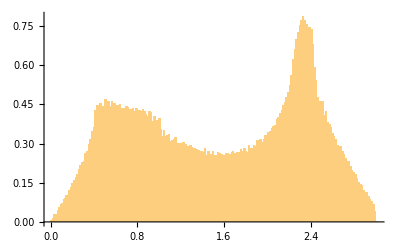

```mathematica
Histogram[Energies1, {"Raw", 200},PDF]
```